# Many Body Simulation Code

Matt Kafker

University of Washington, Seattle

## Many Body Simulations

Run all this code to get started.

## Parameters

```mathematica
dt=0.05;
rad=1;
InverseSquareConstant=-10;
SoftSphereExponent=2;
SoftSphereCoefficient =10;
LJConstant=10;
```

## HardSphere

Classic hard spheres with reflecting boundary conditions.

```mathematica
HardSphere[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest,progress},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];
(*progress=PrintTemporary[ToString[N@counter[[-1]]/steps]<>"%"];
NotebookDelete[progress];*)

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Polydisperse

Polydisperse hard spheres. Note that all spheres still have same mass.

```mathematica
Polydisperse[initialPositions_,initialVelocities_,boxSize_,steps_,radii_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest,progress},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];
(*progress=PrintTemporary[ToString[N@counter[[-1]]/steps]<>"%"];
NotebookDelete[progress];*)

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Rest@Nearest[positions->"Index",positions⟦particle⟧,{∞,2.1Max[radii]}];
Do[
(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest[[n]]⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(radii[[particle]]+radii[[nearest[[n]]]])^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest[[n]],counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest[[n]]⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=radii[[particle]]+radii[[nearest[[n]]]] - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest[[n]]⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest[[n]]⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest[[n]]⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*),
{n,Length[nearest]}]
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-radii[[particle]],
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-radii[[particle]])];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Noisy

Adds rotational diffusion. Only runs in 2D.

```mathematica
Clear[Noisy];
Noisy[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[
velocities[[particle]]=RotationMatrix[RandomVariate[VonMisesDistribution[0,90]]].velocities[[particle]];
(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## ZeroTemp

Spheres push off one another, then stop moving. Useful for generating non-overlapping initial conditions for other simulations.

```mathematica
Clear[ZeroTemp];
ZeroTemp[initialPositions_,initialVelocities_,boxSize_,steps_,rad_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;
velocities=0*velocities;
(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Periodic

Hard sphere simulation with periodic boundary conditions. Not working properly!

```mathematica
Periodic[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)

(*As of June 21, 2021, this is still not working. Particles don't collide at the egde of the box.*)

nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2,DistanceFunction->Function[{u,v},ToroidalSquaredDistance[u,v,boxSize]](*Function[{x,y},#.#&[(If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]])&/@Transpose[{x,y}]]]*)(*Function[{x,y},#.#&[#⟦1⟧-#⟦2⟧-2 boxSize Sign[#⟦1⟧-#⟦2⟧] HeavisideTheta[Abs[#⟦1⟧-#⟦2⟧]-boxSize]&/@Transpose[{x,y}]]]*)


(*
AT PRESENT THIS IS THE FASTEST, BUT SECOND MOST PARSIMONIOUS.
Function[{x,y},#.#&[(If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]])&/@Transpose[{x,y}]]]

(**)Function[{x,y},Norm[If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]]&/@Transpose[{x,y}]]]*)


(*Function[{x,y},Norm[(First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&)/@Transpose[{x,y}]]]*)];

(*How far is the nearest particle?*)
sqdist=ToroidalSquaredDistance[positions⟦particle⟧,positions⟦nearest⟧,boxSize];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=-Table[td[positions⟦particle⟧[[j]],positions[[nearest]][[j]],boxSize],{j,Length[positions⟦particle⟧]}]/dist;(*N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;*)

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];



Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize,
positions⟦particle,dimension⟧+=(-Sign[positions⟦particle,dimension⟧])*2(boxSize)];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

### Distance Function Testing for Toroidal BCs

```mathematica
Range[-5,5]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
Mod[Range[-5,5],5]
```

{0,1,2,3,4,0,1,2,3,4,0}

{{-6,-16},{-8,-18}}

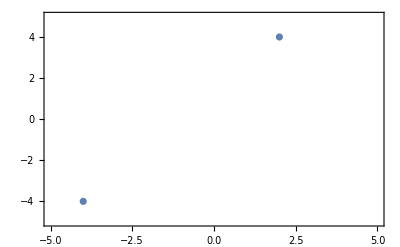

```mathematica
Module[{pos1,pos2,dx,boxSize=5,vec},
pos1={-4,-4};pos2={2,4};
dx=pos1-pos2;
vec=If[Abs[#[[1]]]<Abs[#[[2]]],#[[1]],#[[2]]]&/@Transpose[{dx,dx-2*boxSize}];


(*Print[Abs[vec]];*)
(*Print[{dx,dx-2*boxSize}];*)
Print[Transpose[{dx,dx-2*boxSize}]];

ListPlot[{pos1,pos2},PlotRange->{{-boxSize,boxSize},{-boxSize,boxSize}},Frame->True]
]
```

```mathematica
Abs[{1,1}]<Abs[{1,2}]
```

{1,1}<{1,2}

```mathematica
Norm[{1,1,1,1,1}]
```

√5

Works for x final, y initial.

```mathematica
f[x_,y_,boxSize_]:=First@MinimalBy[{x-y,x-y-2 boxSize,x-y+2boxSize},Abs]
```

```mathematica
f[0.8a,-0.8a,a]
```

-0.4 a

```mathematica
With[{boxSize=a},
First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&[{0.8a,-0.8a}]
]
```

-0.4 a

```mathematica
Transpose[{{1,3,5,7,9},{2,4,6,8,10}}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

This should be our distance function. First, it takes the smallest distance along each axis from {no translation, translation by 2 boxSize, translation by -2 boxSize}. Then

```mathematica
With[{boxSize=a},Norm[(First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&)/@Transpose[{#1,#2}]]&[{-0.8a,-0.8a},{0.8a,0.8a}]
]
```

0.565685 Abs[a]

```mathematica
Sqrt[2*0.4^2]
```

0.565685

Testing that the toroidal distance function is working

```mathematica
With[{boxSize=10},Norm[(First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&)/@Transpose[{#1,#2}]]&[{-9,-9,-9,-9,-9,-9,-9},{9,9,9,9,9,9,9}]]
```

2 √7

Should be equal to

```mathematica
√(7*2^2)
```

2 √7

Indeed it is.

Testing this distance function inside nearest.

```mathematica
With[{boxSize=10},Nearest[{{1,1,1,1,1},{2,2,-2,2,2},{3,3,3,3,3},{1,2,3,4,5},{-9,-9,-9,-9,-9}}->"Index",{9,9,9,9,9},2,DistanceFunction->(Norm[(First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&)/@Transpose[{#1,#2}]]&)]
]
```

{5,3}

```mathematica
Sign[-2]
```

-1

```mathematica
x=5;x+=1
```

6

Trying another, hopefully more efficient distance function.

```mathematica
boxSize=10
```

10

```mathematica
Function[{x,y},Norm[If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]]&/@Transpose[{x,y}]]][{-9,-9,-9,-9,-9,-9,-9},{9,9,9,9,9,9,9}]
```

2 √7

```mathematica
With[{boxSize=10},Nearest[{{1,1,1,1,1},{2,2,-2,2,2},{3,3,3,3,3},{1,2,3,4,5},{-9,-9,-9,-9,-9}}->"Index",{9,9,9,9,9},2,DistanceFunction->Function[{x,y},Norm[If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]]&/@Transpose[{x,y}]]]]
]
```

{5,3}

```mathematica
#.#&[{1,1}]
```

2

```mathematica
Function[{x,y},√(#.#)&[(If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]])&/@Transpose[{x,y}]]][{-9,-9,-9,-9,-9,-9,-9},{9,9,9,9,9,9,9}]
```

2 √7

Yet another function. Perhaps the fastest yet?

```mathematica
Function[{x,y},#.#&[#⟦1⟧-#⟦2⟧-2 boxSize Sign[#⟦1⟧-#⟦2⟧] HeavisideTheta[Abs[#⟦1⟧-#⟦2⟧]-boxSize]&/@Transpose[{x,y}]]][{-9,-9,-9,-9,-9,-9,-9},{9,9,9,9,9,9,9}]/.boxSize->10
```

28

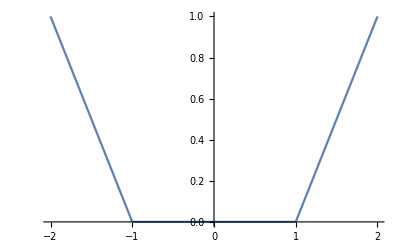

```mathematica
Plot[Ramp[Abs[x]-1],{x,-2,2}]
```

```mathematica
Ramp[Abs[0.9]-1]
```

0.

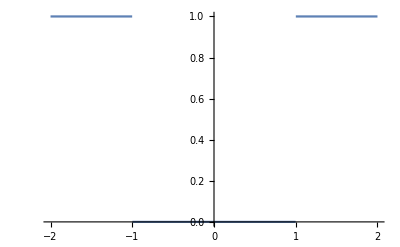

```mathematica
Plot[HeavisideTheta[Abs[x]-1],{x,-2,2}]
```

```mathematica
boxSize=10
```

10

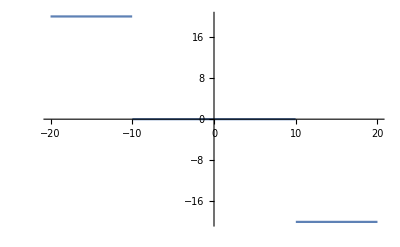

```mathematica
Plot[-2 boxSize Sign[α] HeavisideTheta[Abs[α]-boxSize],{α,-2boxSize,2boxSize}]
```

## ZeroTempPeriodic

Spheres push off one another, then stop moving . Useful for generating non - overlapping initial conditions for other simulations. Periodic boundary conditions. Also not working properly!

```mathematica
ZeroTempPeriodic[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];


(*Update positions*)
positions+=dt*velocities;
velocities*=0;
(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2,DistanceFunction->Function[{x,y},#.#&[(If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]])&/@Transpose[{x,y}]]](*Function[{x,y},#.#&[#⟦1⟧-#⟦2⟧-2 boxSize Sign[#⟦1⟧-#⟦2⟧] HeavisideTheta[Abs[#⟦1⟧-#⟦2⟧]-boxSize]&/@Transpose[{x,y}]]]*)


(*
AT PRESENT THIS IS THE FASTEST, BUT SECOND MOST PARSIMONIOUS.
Function[{x,y},#.#&[(If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]])&/@Transpose[{x,y}]]]

(**)Function[{x,y},Norm[If[Abs[#⟦1⟧-#⟦2⟧]<boxSize,#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2boxSize Sign[#⟦1⟧-#⟦2⟧]]&/@Transpose[{x,y}]]]*)


(*Function[{x,y},Norm[(First[MinimalBy[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦2⟧-2 boxSize,#⟦1⟧-#⟦2⟧+2boxSize},Abs]]&)/@Transpose[{x,y}]]]*)];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];



Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
positions⟦particle,dimension⟧+=(-Sign[positions⟦particle,dimension⟧])*2boxSize];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Infinite

Hard sphere gas with no boundary.

```mathematica
Infinite[initialPositions_,initialVelocities_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];*)



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## InverseSquare

Many body simulation with pairwise inverse-square force.

```mathematica
InverseSquare[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[
velocities[[particle]]+=Total[
If[Norm[#-positions[[particle]]]>0,InverseSquareConstant dt (#-positions[[particle]])/Norm[#-positions[[particle]]]^3,0*#]&/@positions
]
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Lennard-Jones

Many body simulation with pairwise Lennard-Jones potential.

```mathematica
LennardJones[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;

(*Mutual distance checks & scattering for all particles*)
Do[
velocities[[particle]]+=Total[
If[Norm[#-positions[[particle]]]>0,-4LJConstant dt  (-12/Norm[#-positions[[particle]]]^13+6/Norm[#-positions[[particle]]]^7)*(#-positions[[particle]])/Norm[#-positions[[particle]]],0*#]&/@positions
]
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Soft Spheres

Soft sphere simulation. Exponent of soft-sphere potential defined in “Parameters” section above.

```mathematica
SoftSphere[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest,δ},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;
(*velocities*=0;*)

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

velocities[[particle]]+=-dt* SoftSphereExponent *SoftSphereCoefficient(1-dist/(2 rad))^(SoftSphereExponent-1)*(positions[[nearest]]-positions[[particle]])/dist;

(*(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)*)
],
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Dissipative

Hard sphere simulation with a coefficient of restitution less than 1. Not carefully thought through; just playing around.

```mathematica
CoeffOfRest=0.6;
Dissipative[initialPositions_,initialVelocities_,boxSize_,steps_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest},

positions=states[[1]];
velocities=states[[2]];

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Update positions*)
positions+=dt*velocities;


(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
If[0<sqdist<(2.*rad)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rad - dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((velocities⟦nearest⟧-velocities⟦particle⟧).nHat)*nHat;
velocities⟦particle⟧+=CoeffOfRest*Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
velocities⟦nearest⟧-=CoeffOfRest*Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rad,
velocities⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rad)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];



{positions, velocities} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];

(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Flocking

N-body simulation of a flock of birds, following model of Bialek in “Statistical Mechanics for Natural Flocks of Birds”

```mathematica
rbFlock=0.2;
speed=0.05;
ncFlock=7;
αFlock=35;
βFlock=5;
raFlock=0.8;
reFlock=0.5;
r0Flock=1;
```

```mathematica
Flocking[initialPositions_,initialVelocities_,boxSize_,steps_,noise_,avgvel_,force_]:=

Module[{collisions,trajectories, counter},

(*Array to keep track of collisions as they occur*)
collisions={};

(*Array to keep track of the time step. Will just store counting numbers.*)
counter={0};

(*NestList will iteratively apply a function to the original input. In this case, the input will be the initial conditions, and the function will update the positions and velocities. Store trajectories to return at the end.*)
trajectories=Monitor[NestList[
Function[{states},
Module[{positions,velocities,sqdist,nHat,Δv,overlap,dist, nearest,Δt,neighbors,newvels},

positions=states[[1]];
velocities=states[[2]];
newvels=velocities;

(*Increment the counter.*)
AppendTo[counter,counter[[-1]]+1];

(*Treat neighbor interactions*)
Do[
neighbors=Rest@Nearest[positions->"Index",positions⟦particle⟧,ncFlock+1];
(*Print[neighbors];*)
newvels[[particle]]=0;
newvels[[particle]]+=avgvel*αFlock Sum[velocities[[j]],{j,neighbors}];
newvels[[particle]]+=force*βFlock Sum[
Module[{vec,eij,rij},
vec=positions[[particle]]-positions[[j]];
rij=Norm[vec];
eij=vec/rij;
Which[rbFlock<rij<raFlock,1/4(rij-reFlock)/(raFlock-reFlock)*eij,
raFlock<rij<r0Flock,eij,
rij>r0Flock,0,
rij<rbFlock,0]],{j,neighbors}];

,
{particle,1,Length[positions]}];

newvels+=noise*ncFlock*RandomPoint[Sphere[ConstantArray[0,Length@First@initialPositions]],Length@positions];

(*Mutual distance checks & scattering for all particles*)
Do[

(*Find the closest particle to the particle of interest. Take second because closest will be particle itself.*)
nearest=Last@Nearest[positions->"Index",positions⟦particle⟧,2];
(*Print[neighbors];*)

(*How far is the nearest particle?*)
sqdist=SquaredEuclideanDistance[positions⟦particle⟧,positions⟦nearest⟧];

(*If it is close enough to scatter...*)
 If[0<sqdist<(2.*rbFlock)^2,

(*Record collision*)
AppendTo[collisions,{particle,nearest,counter[[-1]]}];

dist=N@√sqdist;

(*Vector along which scattering occurs*)
nHat=N@(positions⟦nearest⟧-positions⟦particle⟧)/dist;

(*Correct disk overlap*)
overlap=2 rbFlock- dist;
positions⟦particle⟧-=(overlap/2)nHat;
positions⟦nearest⟧+=(overlap/2)nHat;

(*How much velocities change during scattering*)
Δv=((newvels⟦nearest⟧-newvels⟦particle⟧).nHat)*nHat;
newvels⟦particle⟧+=Δv;(*(2masses⟦particle2⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
newvels⟦nearest⟧-=Δv;](*(2masses⟦particle1⟧)/(masses⟦particle1⟧+masses⟦particle2⟧)*)
,
{particle,1,Length[positions]}];




(*Reflection off walls. If particle is within "rad" of edge, reverse that component of its velocity. Set its position to be precisely "rad" from the edge. 
Implements this procedure componentwise.*)
Do[

If[Abs[positions⟦particle,dimension⟧]>boxSize-rbFlock,
newvels⟦particle,dimension⟧*=-1;
positions⟦particle,dimension⟧=N[Sign[positions⟦particle,dimension⟧](boxSize-rbFlock)];
];,
{dimension,1,Length[positions⟦1⟧]},
{particle,1,Length[positions]}];

newvels=dt*(Normalize/@newvels);
(*Update positions*)
positions+=newvels;
{positions, newvels} 
]
(*Initial conditions and number of steps, for NestList.*)
],{initialPositions,initialVelocities},steps],"Simulation Progress: "<>ToString[100*N@counter[[-1]]/steps]<>"%"];



(*Return list {trajectories, collisions}.*)
{trajectories, collisions}
]
```

## Control Panel

### Useful Functions (Run these!)

```mathematica
collisionsToScatteringGraph[collisions_]:=Graph[DeleteDuplicates[Sort[#⟦1⟧<->#⟦2⟧]&/@collisions],VertexLabels->"Name"];

collisionsToCausalGraph[collisions_] := Module[{particles, instants, edges},
(*Extract particles from list of collisions*)
  particles = Union @@ collisions[[All, ;; 2]];

(*Generate causal graph from collisions. Construct a directed edge whenever an uninterrupted sequence of two collisions involves the same particle.*)
  edges = Catenate[Function[particle,
      instants = SplitBy[Select[collisions, #[[1]] === particle || #[[2]] === particle &], Last];
      Catenate[BlockMap[DirectedEdge @@@ Tuples[#] &, instants, 2, 1]]
      ] /@ particles];

(*Finally, construct the graph*)
  Graph[DeleteDuplicates@edges,GraphLayout->"LayeredDigraphEmbedding",AspectRatio->1/GoldenRatio,ImageSize->Large,VertexLabels->"Name"]
  ]

Clear[MDistn,x,MDistParam];
MDistn[n_]:=ProbabilityDistribution[1/(2^(-1+n/2) (MDistParam)^(-n/2) Gamma[n/2])v^(n-1)Exp[-(MDistParam v^2)/2],{v,0,∞}];


(*td=FunctionCompile[Function[{Typed[x,"Real64"],Typed[y,"Real64"],Typed[b,"Real64"]},Min[Abs[x-y],Abs[x-y-2b],Abs[x-y+2b]]]];

ToroidalSquaredDistance[u_,v_,boxSize_]:=#.#&@Table[td[N@u[[j]],N@v[[j]],boxSize],{j,Length@u}];*)
```

### Control Panel

Having defined a bunch of different simulations above, this function is the control panel. The goal is to minimize complexity and allow for flexible calls to simulations and flexible requests for output.

```mathematica
ManyBodySimulation[ICs_,num_,dimension_,boxSize_,steps_,model_,output_,radiusrules_]:=
Module[{initialConditions,results,traj,vels,speeds,param,radii},

(*Generate radii for simulation and visualization*)
radii=RandomChoice[radiusrules,num];

(*Allow user input for initial conditions*)
initialConditions=ICs;

(*Randomly distributed positions with randomly distributed velcities*)
If[ICs=="Random",
initialConditions=
N[{RandomReal[{-#,#}&@(boxSize-rad),{num,dimension}],
RandomPoint[Ball[ConstantArray[0,dimension]],num]}]];


(*Try to generate non-overlapping initial conditions. Only works for monodisperse at present.*)
If[ICs=="RandomNonOverlapping",
initialConditions={First[Most[ZeroTemp[RandomReal[{-#,#}&@(boxSize-rad),{num,dimension}],RandomPoint[Ball[ConstantArray[0,dimension]],num],boxSize,400,1.1]]][[All,1]][[-1]],RandomPoint[Ball[ConstantArray[0,dimension]],num]}];


(*Choose which simulation to run. All simulations defined above.*)
Which[
model=="HardSphere",results=HardSphere[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="Periodic",results=Periodic[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="ZeroTemp",results=ZeroTemp[initialConditions[[1]],initialConditions[[2]],boxSize,steps,1.1],

model=="ZeroTempPeriodic",results=ZeroTempPeriodic[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="InverseSquare",results=InverseSquare[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="SoftSphere",results=SoftSphere[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="Infinite",results=Infinite[initialConditions[[1]],initialConditions[[2]],steps],

model=="Noisy",results=Noisy[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="Dissipative",results=Dissipative[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="LennardJones",
results=LennardJones[initialConditions[[1]],initialConditions[[2]],boxSize,steps],

model=="Polydisperse",
results=Polydisperse[initialConditions[[1]],initialConditions[[2]],boxSize,steps,radii],

model=="Flocking",
If[ICs=="Random",
initialConditions=
N[{RandomReal[{-#,#}&@(boxSize/4-rad),{num,dimension}],
RandomPoint[Ball[ConstantArray[0,dimension]],num]}]];
results=Flocking[initialConditions[[1]],initialConditions[[2]],boxSize,steps,1,1,1]
];

(*Choose desired output*)
Which[

(*Return all simulation data (i.e. positions, velocities, collisions)*)
output=="All",results,

(*Return positions and velocities organized by time (i.e. all particles' positions and velocities for each time step)*)
output=="TrajectoriesByTime",Catenate@Most[results],

(*Return positions and velocities organized by particle*)
output=="TrajectoriesByParticle",Transpose[Transpose/@Catenate@Most[results]],

(*Return positions organized by time*)
output=="PositionsByTime",Catenate[Most[results]][[All,1]],

(*Return velocities organized by time*)
output=="VelocitiesByTime",Catenate[Most[results]][[All,2]],

(*Return positions organized by particle*)
output=="PositionsByParticle",Catenate[Most[results]][[All,1]]//Transpose,

(*Return velocities organized by particle*)
output=="VelocitiesByParticle",Catenate[Most[results]][[All,2]]//Transpose,

(*Return just collisions of the form (Subscript[particle, 1], Subscript[particle, 2],time)*)
output=="Collisions",results//Last,

(*Generate visualization of simulation. Automatically chooses how to visualize based on simulation dimension*)
output=="Visualize",
Which[dimension==1,traj=Catenate[Most[results]][[All,1]]//Transpose;Manipulate[Graphics[{
{Blue,Opacity[0.3],Line[{{-boxSize,0},{boxSize,0}}]},
{Blue,Opacity[0.3],Line[{{-boxSize,-boxSize/2},{-boxSize,boxSize/2}}]},
{Blue,Opacity[0.3],Line[{{boxSize,-boxSize/2},{boxSize,boxSize/2}}]},
Table[{Gray,Opacity[0.5],Disk[{traj[[n,t]][[1]],0},radii[[n]]]},{n,num}]
},PlotRange->{1.1{-boxSize,boxSize},0.5{-boxSize,boxSize}}],
{t,1,Length[traj⟦1⟧],1},SaveDefinitions->True],

dimension==2,traj=Catenate[Most[results]][[All,1]]//Transpose;
Manipulate[Graphics[{,Table[{Gray,Opacity[0.5],Disk[traj[[n,t]],radii[[n]]]},{n,num}]},PlotRange->1.1{{-boxSize,boxSize},{-boxSize,boxSize}}],
{t,1,Length[traj⟦1⟧],1},SaveDefinitions->True],

dimension==3,traj=Catenate[Most[results]][[All,1]]//Transpose;Manipulate[
Graphics3D[Table[Ball[traj[[n,t]],radii[[n]]],{n,num}]
(*Ball[#,rad]&/@traj⟦All,t⟧*),
PlotRange->{{-boxSize,boxSize},{-boxSize,boxSize},{-boxSize,boxSize}}],
{t,1,Length[traj⟦1⟧],1},SaveDefinitions->True]],

(*Return total kinetic energy of system over time*)
output=="KineticEnergy", Total/@Map[Norm[#]^2/2&,Catenate[Most[results]][[All,2]],{2}],

(*Return final frame of visualization without visualizing other frames*)
output=="FinalFrame",traj=Catenate[Most[results]][[All,1]][[-1]];Graphics[{,Table[{Gray(*If[radii[[n]]==1,RGBColor["#042A2B"],RGBColor["#5EB1BF"]]*),Opacity[0.5],Disk[traj[[n]],radii[[n]]]},{n,num}]},PlotRange->1.1{{-boxSize,boxSize},{-boxSize,boxSize}}],

(*Return causal graph of simulation*)
output=="CausalGraph",collisionsToCausalGraph[Last@results],

(*Make histogram of speed distribution for each particle, perform a parameter fit to estimate the temperature.*)
output=="MeasureTemp",vels=Catenate[Most[results]][[All,2]];
ParallelTable[
(*Find dimensionless temperature that fits particle's speed distribution best*)
speeds=Norm/@vels[[All,particle]];
param=FindDistributionParameters[speeds,MDistn[dimension]];
Show[(*Make histogram of speeds*)
Histogram[speeds,20,"PDF",PlotRange->Automatic(*{{0,5*StandardDeviation[speeds]},Automatic}*),PlotLabel->Style[ToString[dimension]<>"D, "<>ToString[num]<>" Particles, "<>ToString[steps]<>" steps, Box Size = "<>ToString[boxSize]<>"\nParticle "<>ToString[particle]<>": k_BT/m = "<>ToString[(1/MDistParam)/.param],Black,14],ImageSize->400,Frame->True,FrameLabel->{Style["Speed",Black,12],Style["PDF",Black,12]}],
(*Plot Maxwell-Boltzmann speed distribution over histogram, with fitted dimensionless temp parameter*)
Plot[(PDF[MDistn[dimension],v]/.param),{v,0,Max[speeds]}]
],{particle,num}],


(*Output scattering graph––nodes are particles and edges indicate collisions*)
output=="ScatteringGraph",collisionsToScatteringGraph[Last@results],

(*Same as "Visualize" above, but saves movie to desktop*)
output=="Movie",
Which[dimension==1,traj=Catenate[Most[results]][[All,1]]//Transpose ;Export["~/Desktop/"<>model<>"-"<>ToString[dimension]<>"D-Steps"<>ToString[steps]<>"-Particles"<>ToString[num]<>"-dt"<>ToString[dt]<>"-Boxsize"<>ToString[boxSize]<>".mp4",Table[Graphics[{
{Blue,Opacity[0.3],Line[{{-boxSize,0},{boxSize,0}}]},
{Blue,Opacity[0.3],Line[{{-boxSize,-boxSize/2},{-boxSize,boxSize/2}}]},
{Blue,Opacity[0.3],Line[{{boxSize,-boxSize/2},{boxSize,boxSize/2}}]},
Table[{Gray,Opacity[0.5],Disk[{traj[[n,t]][[1]],0},radii[[n]]]},{n,num}]},PlotRange->{1.1{-boxSize,boxSize},0.5{-boxSize,boxSize}}],
{t,1,Length[traj⟦1⟧],1}],"FrameRate"->Floor[steps/10]],

dimension==2,traj=results⟦1,All,1⟧ᵀ ;Export["~/Desktop/"<>model<>"-"<>ToString[dimension]<>"D-Steps"<>ToString[steps]<>"-Particles"<>ToString[num]<>"-dt"<>ToString[dt]<>"-Boxsize"<>ToString[boxSize]<>".mp4",Table[Graphics[{,Table[{If[radii[[n]]==1,RGBColor["#042A2B"],RGBColor["#5EB1BF"]],Opacity[0.5],Disk[traj[[n,t]],radii[[n]]]},{n,num}]},PlotRange->1.1{{-boxSize,boxSize},{-boxSize,boxSize}}],
{t,1,Length[traj⟦1⟧],1}],"FrameRate"->Floor[steps/10]]],

(*Same as "TrajectoriesByParticle", but saves data to a .csv file on desktop*)
output=="SaveTrajectoriesByParticle",Export["~/Desktop/"<>model<>"-"<>ToString[dimension]<>"D-Steps"<>ToString[steps]<>"-Particles"<>ToString[num]<>"-dt"<>ToString[dt]<>"-Boxsize"<>ToString[boxSize]<>".csv",Transpose[Transpose/@Catenate@Most[results]]]

]

]
```

## Visualization & Test Cases

## 1D Visualizations

A few sample visualizations

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)25,
(*Dimension: *) 1,
(*Box Size: *)30,
(*Steps: *)1000, 
(*Model: *) "HardSphere", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)25,
(*Dimension: *) 1,
(*Box Size: *)30,
(*Steps: *)1000, 
(*Model: *) "LennardJones", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)15,
(*Dimension: *) 1,
(*Box Size: *)30,
(*Steps: *)1000, 
(*Model: *) "Polydisperse", 
(*Output: *) "Visualize",
  (*Radius Rules*){0.85,0.15}->{1,5}]
```

## 2D Visualizations

Same visualizations in 2D

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)15,
(*Dimension: *) 2,
(*Box Size: *)10,
(*Steps: *)1000, 
(*Model: *) "InverseSquare", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"Random" ,
(*Num: *)200,
(*Dimension: *) 2,
(*Box Size: *)30,
(*Steps: *)1000, 
(*Model: *) "Flocking", 
(*Output: *) "Visualize",
  (*Radius Rules*){rbFlock}]
```

## 3D Visualizations

Sample 3D visualization

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)25,
(*Dimension: *) 3,
(*Box Size: *)5,
(*Steps: *)1000, 
(*Model: *) "Infinite", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

## Test Energy Conservation

Plot kinetic energy over time for hard sphere simulation. Also shows that simulation behaves as expected in higher dimensions.

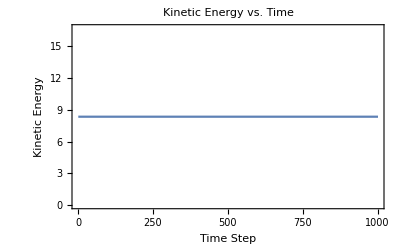

```mathematica
ListLinePlot[ManyBodySimulation[
(*Initial Conditions: *)"RandomNonOverlapping" ,
(*Num: *)25,
(*Dimension: *) 7,
(*Box Size: *)30,
(*Steps: *)1000, 
(*Model: *) "HardSphere", 
(*Output: *) "KineticEnergy",
  (*Radius Rules*){1}],Frame->True,FrameLabel->{"Time Step","Kinetic Energy"},PlotLabel->"Kinetic Energy vs. Time"]
```

## Test Momentum Conservation

Is momentum conserved during particle-particle collisions?

```mathematica
ManyBodySimulation[
(*Initial Conditions: *){{#,0}&/@Range[-(boxSize-2rad),(boxSize-2rad),4*rad],Table[{KroneckerDelta[n,1],0},{n,Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]]}]} ,
(*Num: *)Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]],
(*Dimension: *) 2,
(*Box Size: *)10,
(*Steps: *)1000, 
(*Model: *) "HardSphere", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

## Test Newton's Cradle

Same as test above, but for “solid” collision.

```mathematica
ManyBodySimulation[
(*Initial Conditions: *){{#,0}&/@Range[-(20-8rad),(20-8rad),2*rad],Table[{KroneckerDelta[n,1],0},{n,Length[Range[-(20-8rad),(20-8rad),2*rad]]}]} ,
(*Num: *)Length@Range[-(20-8rad),(20-8rad),2*rad],
(*Dimension: *) 2,
(*Box Size: *)20,
(*Steps: *)1000, 
(*Model: *) "HardSphere", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

## Test N-Dimensional Motion

Does “simulate” behave well in N-dimensions? To test this, send particles along N cardinal axes, and measure their positions in time. We should see triangular curves for reflecting boundary conditions.

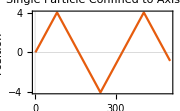
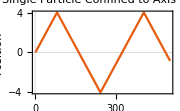
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{dimension=10},
Table[
ListLinePlot[Catenate[ManyBodySimulation[
(*Initial Conditions: *){{Table[0,dimension]},{Table[KroneckerDelta[n,d],{n,dimension}]}} ,
(*Num: *)1,
(*Dimension: *) dimension,
(*Box Size: *)5,
(*Steps: *)500, 
(*Model: *) "HardSphere", 
(*Output: *) "PositionsByTime",
  (*Radius Rules*){1}]][[All,d]],PlotTheme->"Scientific",PlotLabel->"Single Particle Confined to Axis #" <>ToString[d],ImageSize->Small,FrameLabel->{"Time","Position"}],
{d,dimension}]
]
```

## Test Causal Graph from “testMomentum”

Run simple simulation and display causal graph next to it.

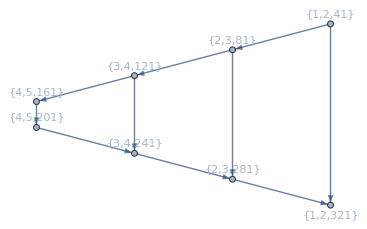

```mathematica
Row[{ManyBodySimulation[
(*Initial Conditions: *){{#,0}&/@Range[-(boxSize-2rad),(boxSize-2rad),4*rad],Table[{KroneckerDelta[n,1],0},{n,Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]]}]} ,
(*Num: *)Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]],
(*Dimension: *) 2,
(*Box Size: *)10,
(*Steps: *)400, 
(*Model: *) "HardSphere", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}],
ManyBodySimulation[
(*Initial Conditions: *){{#,0}&/@Range[-(boxSize-2rad),(boxSize-2rad),4*rad],Table[{KroneckerDelta[n,1],0},{n,Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]]}]} ,
(*Num: *)Length[Range[-(boxSize-2rad),(boxSize-2rad),4*rad]],
(*Dimension: *) 2,
(*Box Size: *)10,
(*Steps: *)400, 
(*Model: *) "HardSphere", 
(*Output: *) "CausalGraph",
  (*Radius Rules*){1}]}]
```

## Pool Simulation

A fun example: use ManyBodySimulation to simulate a break in pool.

```mathematica
(*Colors of pool balls*)
colors={Yellow,Blue,Red,Purple,Orange,Green,RGBColor["#800000"],Black};

(*Define graphics for stripes, solids, and cue ball*)
stripes[pos_,rad_,color_,number_]:={{Black,Circle[{pos[[1]],pos[[2]]},rad]},{White,Disk[{pos[[1]],pos[[2]]},0.99rad]},{color,Rectangle[{pos[[1]]-0.915rad,pos[[2]]-0.4rad},{pos[[1]]+0.915rad,pos[[2]]+0.4rad}]},
{White,Disk[{pos[[1]],pos[[2]]},0.3rad]},

{color,Polygon[Table[{pos[[1]]+0.99rad Cos[θ],pos[[2]]+0.99rad Sin[θ]},{θ,-ArcTan[0.41/0.92],ArcTan[0.41/0.92],0.005}]]},

{color,Polygon[Table[{pos[[1]]+0.99rad Cos[θ],pos[[2]]+0.99rad Sin[θ]},{θ,π-ArcTan[0.4/0.915],π+ArcTan[0.4/0.915],0.01}]]},

{Text[number,pos]}};

solids[pos_,rad_,color_,number_]:={{Black,Circle[pos,rad]},{White,Disk[pos,0.3rad]},{color,Annulus[pos,{0.3rad,0.99rad}]},{Text[number,pos]}};

cue[pos_,rad_]:={{Black,Circle[pos,rad]},{White,Disk[pos,0.99rad]},{Red,Disk[pos,0.2rad]}};

(*Run simulation and animate results*)
Module[{traj,billiards,boxSize=10,steps=100,model="HardSphere"},

(*Initial positions of balls in the triangle*)
billiards=RandomSample[Catenate@Prepend[Table[2row{-Cos[π/3]+col/row,Sin[π/3]},{row,1,4},{col,0,row}],{{0,0}}]];

(*Run simulation, including cue ball with small random perturbations to the break*)
traj=ManyBodySimulation[{Prepend[billiards,{0,-8}+RandomReal[{-0.1,0.1},2]],Prepend[0*billiards,{0,10}+RandomReal[{-0.1,0.1},2]]},Length[colors],2,boxSize,steps,model,"All",{1}][[1,All,1]];

(*Animate evolution*)
Manipulate[
Graphics[
{{FaceForm[RGBColor["#0a6c03"]],EdgeForm[Black],Rectangle[{-boxSize,-boxSize},{boxSize,boxSize}]},
cue[traj[[t,1]],1],
Join[Table[solids[traj[[t,n+1]],rad,colors[[n]],n],{n,Length[colors]}],
Table[stripes[traj[[t,8+n+1]],rad,colors[[n]],n+8],{n,Length[colors]-1}]]
},ImageSize->500,PlotRange->{{-boxSize,boxSize},{-boxSize,boxSize}}
],
{t,1,steps,1}]
]
```

## Thermodynamics

## Temperature from Speed Distributions

We will measure the temperature of the hard sphere system by fitting individual particle speed distributions to the Maxwell-Boltzmann speed distribution. This distribution has one parameter, which is proportional to temperature.

### Maxwell-Boltzmann Speed Distribution

#### Derivation

In statistical mechanics, the probability that a system at temperature T will be found in a given state with energy E is given by

where N is a normalization constant and k_B is Boltzmann’s constant.

A hard sphere in n-dimensions with velocity  has energy is given by

So, the probability that any given hard sphere will be found with this energy is

This is known as the Maxwell-Boltzmann velocity distribution.

For our purposes, it will be most convenient to consider a particle’s distribution of speeds rather than velocities. To derive this from the Maxwell-Boltzmann velocity distribution, we can switch to spherical coordinates and integrate over all coordinates except the radial coordinate. This will leave us with

	
	
where v is the particle’s speed and N' is a new normalization constant. The  term comes from the radial part of the Jacobian in our new coordinate system.

All that remains is to find the normalization constant:

```mathematica
Assuming[{n∈PositiveIntegers,α≥0},∫_0^∞ x^(n-1)Exp[-(α x^2)/2]ⅆx]
```

2^(-1+n/2) α^(-n/2) Gamma[n/2]

#### Define Distribution

We define the Maxwell-Boltzmann speed distribution for n dimensions. We have now substituted 1/α = (k_B T)/m.

```mathematica
Clear[MDistn,x];
MDistn[n_]:=ProbabilityDistribution[1/(2^(-1+n/2) (α)^(-n/2) Gamma[n/2])x^(n-1)Exp[-(α x^2)/2],{x,0,∞}];
```

### Measure Temperature from Speed Distributions of Particles in Time

Run a simulation. Plot a histogram of each particle’s speed distribution over the course of the simulation. Fit parameter α = m/(k_B T) to each distribution.

Sample simulation

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"Random" ,
(*Num: *)15,
(*Dimension: *) 2,
(*Box Size: *)5,
(*Steps: *)500, 
(*Model: *) "HardSphere", 
(*Output: *) "Visualize",
  (*Radius Rules*){1}]
```

Run large simulation, and fit parameter to estimate temperature. Fitting is parallelized, but can still take a while.

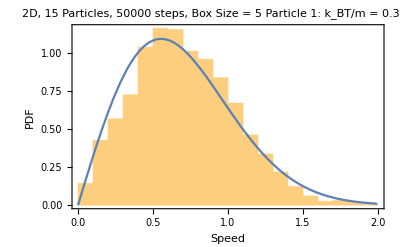
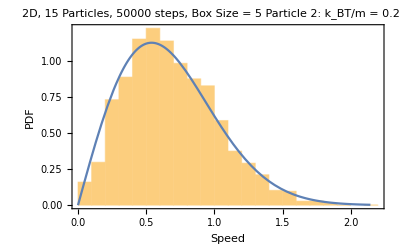
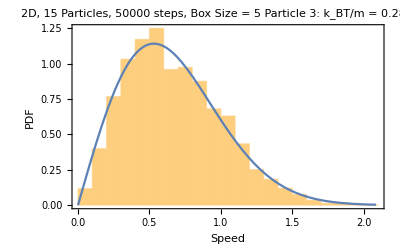
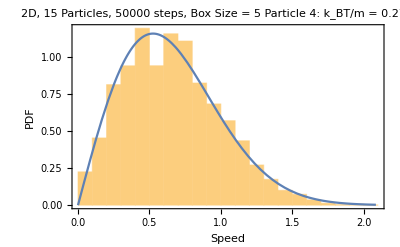
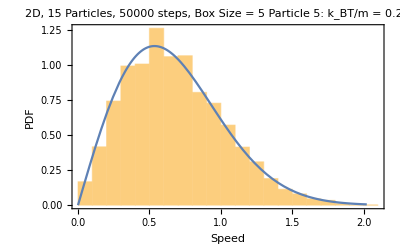
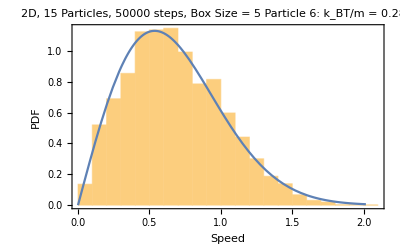
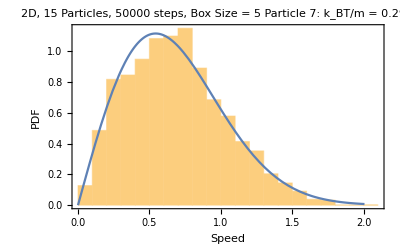
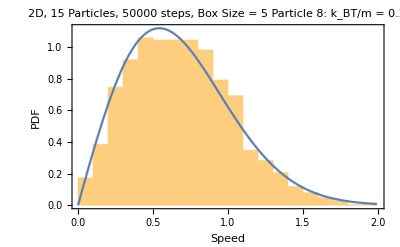

```mathematica
ManyBodySimulation[
(*Initial Conditions: *)"Random" ,
(*Num: *)15,
(*Dimension: *)2,
(*Box Size: *)5,
(*Steps: *)50000, 
(*Model: *) "HardSphere", 
(*Output: *) "MeasureTemp",
  (*Radius Rules*){1}]
```

## Pressure (Not yet implemented)

We determine the pressure using the formula
	⟨P⟩ = 1/(A Δt)∑_j Δv_j^⊥
which comes from F = m Δv/Δt, where m = 1, and Δv_j^⊥ refers to the change in the normal component of the velocity when particle j hits the wall.

We measure the pressure as follows.
	1.) Choose one wall of a 3D box.
	2.) Record all Δv_j^⊥ for collisions with that wall, as well as the time of collision.
	3.) Choose a value for Δt, group the collisions by time in intervals of size Δt.
	4.) Plug into the formula for ⟨P⟩ above for each collection of collisions.
	5.) Plot a histogram of the results.

## Causal Graphs

## Measuring Temperature from Collision Rate

Can we understand the thermodynamics of hard sphere systems directly from the causal graph?

### Useful Functions (not up to date)

Count the number of collisions over time in the simulation.

```mathematica
CountNodes[graph_]:=Module[{vertices,t0,nodeslist,counts,tmax,τ},

(*Extract collisions from causal graph*)
vertices=VertexList[graph];

(*Extract times of first and last collisions, divide (arbitrarily) into 20 chunks*)
t0=First[MinimalBy[vertices,Last]][[3]];
tmax=First[MaximalBy[vertices,Last]][[3]];
τ=Floor[tmax/20];

(*Extract ordered pair (time, number of collisions which have occurred by that time)*)
nodeslist=Table[{n τ,Select[vertices,#[[3]]<t0+n τ&]},{n,0.8Floor[tmax/τ]}];
counts={#[[1]],Length@#[[2]]}&/@nodeslist
(*ListPlot[counts,Frame->True,FrameLabel->{Style["Time",Black],Style["Number of Collisions",Black]},PlotLabel->Style["Number of Collisions over Time",Black],ImageSize->400,AspectRatio->1]*)];
```

Measure collision rate given a list of pairs (t, # collisions by time t).

```mathematica
MeasureCollisionRate[counts_]:=FindFit[counts,m*x,m,x];
```

Run simulation, extract temp and collision data.

```mathematica
TempVsRate[initSpeeds_,IPs_,IVs_,boxSize_,steps_,dimension_,num_]:=Module[{sim,vels,Ts={},collsVsTime,speeds,param,histograms={},αTemp},

(*Run simulation*)
sim=HardSphereSimulation[IPs,initSpeeds* IVs,boxSize,steps,"Reflecting"];
Print["One simulation Completed."];
(*Gather velocities*)
vels=sim[[1,All,2]];

Do[
speeds=Norm/@vels[[All,particle]];

(*Fit temperature to speeds*)
αTemp=FindDistributionParameters[speeds,MDistn[dimension]];

(*Record temperature*)
AppendTo[Ts,αTemp];

(*Generate histogram associated with the temperature*)
AppendTo[histograms,
Show[
(*Make histogram of speeds*)
Histogram[Norm/@vels[[All,particle]],50,"PDF",PlotRange->Automatic,PlotLabel->Style[ToString[dimension]<>"D, "<>ToString[num]<>" Particles, "<>ToString[steps]<>" steps, Box Size = "<>ToString[boxSize]<>"\nParticle "<>ToString[particle]<>": k_BT/m = "<>ToString[(1/α)/.αTemp],Black,14],ImageSize->400,Frame->True,FrameLabel->{Style["Speed",Black,12],Style["PDF",Black,12]}],

(*Plot Maxwell-Boltzmann speed distribution over histogram, with fitted dimensionless temp parameter*)
Plot[(PDF[MDistn[dimension],v]/.αTemp),{v,0,Max[speeds]}]
]
];
Print["Temp found for particle "<>ToString[particle]<>" of "<>ToString[num]<>"."];
,{particle,num}];

collsVsTime=CountNodes[collisionsToCausalGraph[sim[[2]]]];
{collsVsTime,Ts,Iconize@histograms}]
```

Given temperature and rate data, extract collision rate r, and mean + std of temps.

```mathematica
ExtractRatesTemps[data_]:=
{Flatten@(Values@MeasureCollisionRate[#[[1]]]&/@data),Flatten@Table[Mean[1/#&/@(Values@datum[[2]])],{datum,data}],
Flatten@Table[StandardDeviation[1/#&/@(Values@datum[[2]])],{datum,data}]};
```

Combine previous functions together. Run simulation, and extract plot of T vs. r^2.

```mathematica
TempVsCollisionRate[]:=Module[{dimension,num,boxSize,IVs,IPs,steps,data,rates,temps,initSpeeds,stds,fit},
SeedRandom[10];
dimension=2;
num=15;
boxSize=5;
IVs=RandomPoint[Circle[ConstantArray[0,dimension]],num];
IPs=RandomReal[{-#,#}&@(boxSize-rad),{num,dimension}];
steps=200000;

data={};
initSpeeds=Table[RandomReal[r,num],{r,0.5,5,0.5}];

Do[Print[r];
AppendTo[data,TempVsRate[initSpeeds[[r]],IPs,IVs,boxSize,steps,dimension,num]];,
{r,Length[initSpeeds]}];

{rates,temps,stds}=ExtractRatesTemps[data];
fit=MeasureCollisionRate[Transpose[{rates^2,temps}]];
{rates,temps,stds,data,Show[
ListPlot[Table[{rates[[n]]^2,Around[temps[[n]],stds[[n]]]},{n,Length[temps]}],],
Plot[m*x/.fit,{x,0,70},PlotStyle->Directive[Gray,Dashed]]]}
]
```

### Test Useful Functions

#### Test CountNodes

Same as testMomentum from above, except display the collision rate as well, so we can compare it to a well-understood simulation.

```mathematica
testGraphs2[steps_,boxSize_,model_]:=
Module[{collisions, initialPositions,initialVelocities,graph},

(*Generate linearly spaced positions of balls, with only one of them moving so that it will collide with stationary balls.*)
initialPositions={#,0}&/@Range[-(boxSize-2rad),(boxSize-2rad),4*rad];
initialVelocities=Table[{KroneckerDelta[n,1],0},{n,Length[initialPositions]}];

(*Simulate the evolution*)
collisions=HardSphereSimulation[initialPositions,initialVelocities,boxSize,steps,model][[2]];
(*Print[collisions];*)
(*From the evolution, derive the corresponding causal graph or scattering graph*)
graph=collisionsToCausalGraph[collisions];
{graph,CountNodes[graph]}
]
```

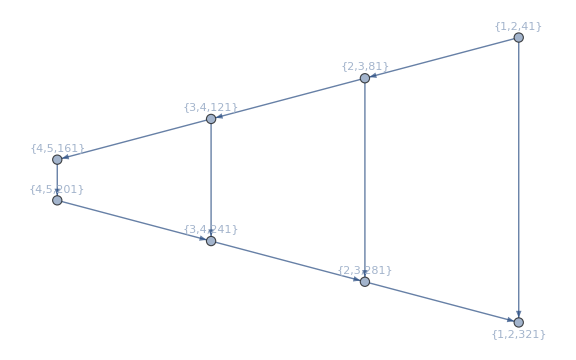
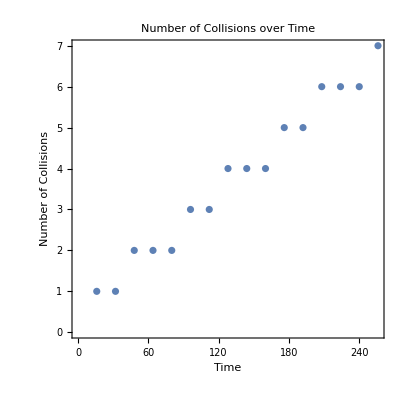

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Column[{testMomentum[400, 10,"Reflecting"],
Row[{Graph[testGraphs2[400, 10,"Reflecting"][[1]],VertexLabels->Automatic],
ListPlot[testGraphs2[400, 10,"Reflecting"][[2]],Frame->True,FrameLabel->{Style["Time",Black],Style["Number of Collisions",Black]},PlotLabel->Style["Number of Collisions over Time",Black],ImageSize->400,AspectRatio->1,
Epilog->{(*Line[{{21,0},{21,12}}],Line[{{41,0},{41,12}}],Line[{{61,0},{61,12}}],Line[{{81,0},{81,12}}],Line[{{101,0},{101,12}}]*)}]}]}]
```

#### Test MeasureCollisionRate

Generate test data with known slope plus minor noise. MeasureCollisionRate is simply a regression.

```mathematica
MeasureCollisionRate@Table[{n,√2 n+RandomVariate[NormalDistribution[0,0.01]]},{n,100}]
```

{r→1.41421}

```mathematica
√2//N
```

1.41421

#### Test TempVsRate

```mathematica
dimensionTVR=2;
numTVR=15;
boxSizeTVR=5;
IVsTVR=RandomPoint[Circle[ConstantArray[0,dimensionTVR]],numTVR];
IPsTVR=RandomReal[{-#,#}&@(boxSizeTVR-rad),{numTVR,dimensionTVR}];
stepsTVR=20000;
initSpeedsTVR=RandomReal[1,numTVR];
```

```mathematica
TempVsRate[initSpeedsTVR,IPsTVR,IVsTVR,boxSizeTVR,stepsTVR,dimensionTVR,numTVR]
```

One simulation Completed.

Temp found for particle 1 of 15.

Temp found for particle 2 of 15.

Temp found for particle 3 of 15.

Temp found for particle 4 of 15.

Temp found for particle 5 of 15.

Temp found for particle 6 of 15.

Temp found for particle 7 of 15.

Temp found for particle 8 of 15.

Temp found for particle 9 of 15.

Temp found for particle 10 of 15.

Temp found for particle 11 of 15.

Temp found for particle 12 of 15.

Temp found for particle 13 of 15.

Temp found for particle 14 of 15.

Temp found for particle 15 of 15.

```mathematica
{{{1000,581},{2000,1072},{3000,1517},{4000,1967},{5000,2448},{6000,2931},{7000,3410},{8000,3865},{9000,4334},{10000,4808},{11000,5283},{12000,5766},{13000,6244},{14000,6698},{15000,7142},{16000,7593}},{{α->6.78173945023884},{α->6.902340968637815},{α->6.747381151190147},{α->7.6670391916043075},{α->7.202009778591531},{α->7.604977116772357},{α->6.1696990164888685},{α->7.072839920500653},{α->7.260697902565891},{α->6.894664502664633},{α->6.670280537241291},{α->6.325681519176856},{α->6.565131171888711},{α->7.233585952843433},{α->7.0968882437704925}},}
```

Ran a sample simulation. Can uniconize histograms to look at them.

#### Test ExtractRatesTemps

Call TempVsRate to generate simulation data.

Why are we using symmetric measures of temperature (i.e. mean and std)? Should we instead use max and 95% interval, or something like that? These distributions are skewed!

```mathematica
testERT=%90
```

{{{1000,581},{2000,1072},{3000,1517},{4000,1967},{5000,2448},{6000,2931},{7000,3410},{8000,3865},{9000,4334},{10000,4808},{11000,5283},{12000,5766},{13000,6244},{14000,6698},{15000,7142},{16000,7593}},{{α→6.78174},{α→6.90234},{α→6.74738},{α→7.66704},{α→7.20201},{α→7.60498},{α→6.1697},{α→7.07284},{α→7.2607},{α→6.89466},{α→6.67028},{α→6.32568},{α→6.56513},{α→7.23359},{α→7.09689}},}

First check, do values of 1/α agree with histograms?

```mathematica
1/#&/@(Values@testERT[[2]])
```

{{0.147455},{0.144878},{0.148206},{0.130428},{0.13885},{0.131493},{0.162082},{0.141386},{0.137728},{0.14504},{0.149919},{0.158086},{0.15232},{0.138244},{0.140907}}

Yes, the values agree.

Now compute collision rate

```mathematica
MeasureCollisionRate[testERT[[1]]]
```

{r→0.479755}

### Increasing Temperature Leads to Increased Slope (not up to date, but image are still useful)

Given a causal graph, can we determine a system’s temperature from the rate at which collisions occur over time?

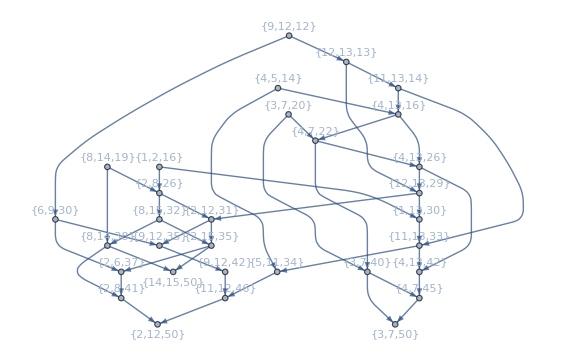

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
Row[{Visualize[15,150,5,"Reflecting"],Graph[genCausalGraph[15,50,5,2,"Reflecting"],VertexLabels->Automatic]}]
```

By counting collisions over time for such a system, we observe a strong linear trend.

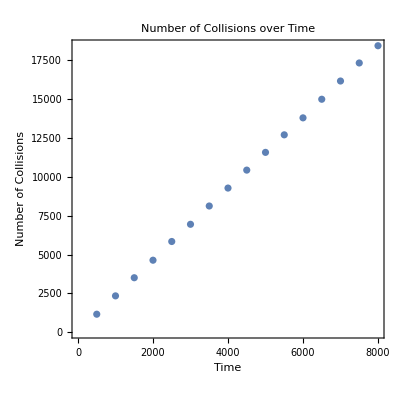

```mathematica
With[{g=genCausalGraph[15,10000,2,5,"Reflecting"]},
ListPlot[CountNodes[g],Frame->True,FrameLabel->{Style["Time",Black],Style["Number of Collisions",Black]},PlotLabel->Style["Number of Collisions over Time",Black],ImageSize->400,AspectRatio->1]]
```

And by increasing the average initial velocity, we see that collision rate increases as well.

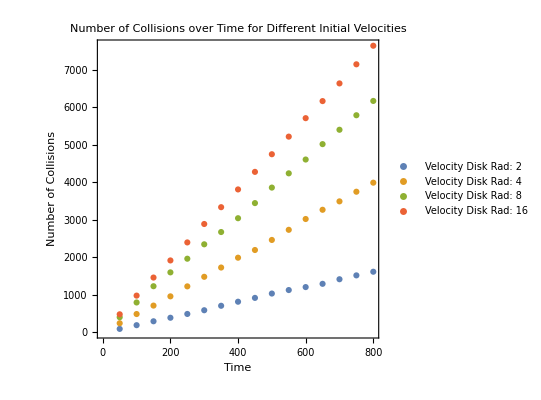

```mathematica
ListPlot[Table[Module[{g,startingNodes},
g=genCausalGraph2[15,1000,5,2,"Reflecting",2^n];
CountNodes[g]],{n,4}],Frame->True,FrameLabel->{Style["Time",Black],Style["Number of Collisions",Black]},PlotLabel->Style["Number of Collisions over Time for Different Initial Velocities",Black],ImageSize->400,PlotLegends->Table["Velocity Disk Rad: "<>ToString[2^m],{m,4}],AspectRatio->1]
```

Thus, it seems possible that the slope of this line––the collision rate r––contains information about the system’s temperature. We construct a systematic test to determine the relationship between the collision rate and the temperature.

### Results

We fix the initial positions and directions of the hard spheres. We then increase average initial speeds, run simulations (20,000 steps, 15 particles, boxSize 5, dimension 2), and measure temperature and collision rate. We observe the result below.

#### Simulation Results

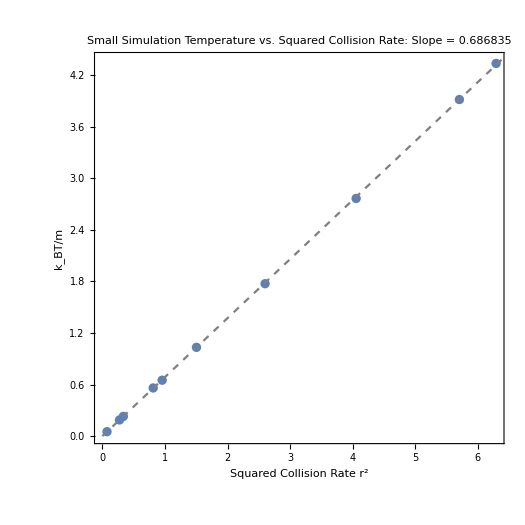

## Tinkering